## 6 - ring Hubbard model

6 - Hubbard model ring

#### Basis for the sector with Sz sector (s1,s2)

```mathematica
n=6;
u=1.25(*1.23*);
occ=6;
base=.;
start={};
end={};
sectors={};
j=0;

For[s1=0,s1<=n,s1++,
If[s1>occ,Continue[]];
	If[occ <=n,
		s2=occ-s1,
		While[s1+n <occ,s1++];
		s2=occ-s1];
	k=0;
	AppendTo[start,j+1] ;
	For[i=0,i<4^n,i++,
		vec=IntegerDigits[i,2,2 n];
		n1=Total[Take[vec,{1,n}]];
		n2=Total[Take[vec,{n+1,2 n}]];
		If[n2==s2&&n1==s1,j++;
			k++;
			base[j]=vec
		]
	];
	AppendTo[end,j];
	AppendTo[sectors,k]
];
size=j;
```

#### Basis size

```mathematica
size
sectors
start
end
```

924

{1,36,225,400,225,36,1}

{1,2,38,263,663,888,924}

{1,37,262,662,887,923,924}

#### Some diagonal operators: double occupancy in site i, Sz in site i, ...

```mathematica
up[x_]:=Take[x,{1,n}];
dn[x_]:=Take[x,{n+1,2 n}];
nn[x_]:=Total[up[x]*dn[x]];
norm[x_]:=Total[Abs[x]];

Double[m_,i_]:=DiagonalMatrix[
Table[base[k][[i]]*base[k][[i+n]],{k,start[[m]],end[[m]]}]
];
DoubleSiteAvg[n_]:=Total[Table[Double[n,i],{i,1,n}]]/n;
OpSz[m_,i_]:=DiagonalMatrix[
Table[base[k][[i]]-base[k][[i+n]],{k,start[[m]],end[[m]]}]
];
SzTot[m_]:=Sum[OpSz[m,i],{i,1,n}];
OpSzSz11[m_]:=OpSz[m,1].OpSz[m,1]
OpSzSz12[m_]:=OpSz[m,1].OpSz[m,2];
OpSzSz13[m_]:=OpSz[m,1].OpSz[m,3];
OpSzSz14[m_]:=OpSz[m,1].OpSz[m,4];
SzTot2[m_]:=SzTot[m].SzTot[m];
```

```mathematica
Table[{OpSzSz12[i]//MatrixForm,OpSzSz13[i]//MatrixForm},{i,1,3}]//MatrixForm
```

#### Hopping matrix

```mathematica
hop=Join[
	Table[i+j,{i,1,n-1},{j,0,1}],
	Table[i-j,{i,2,n},{j,0,1}],{{n,1},{1,n}},
	Table[i+j,{i,n+1,2 n-1},{j,0,1}],
	Table[i-j,{i,n+2,2 n},{j,0,1}],{{2 n,n+1},{n+1,2 n}}
];
Length[hop]
hop
```

24

{{1,2},{2,3},{3,4},{4,5},{5,6},{2,1},{3,2},{4,3},{5,4},{6,5},{6,1},{1,6},{7,8},{8,9},{9,10},{10,11},{11,12},{8,7},{9,8},{10,9},{11,10},{12,11},{12,7},{7,12}}

#### Hopping Hamiltonian in many-body Basis

```mathematica
HopTest[i_,j_,cre_,anh_]:=
	norm[base[i]-base[j]]==2&&
	base[i][[cre]]==1&&
	base[i][[anh]]==0&&
	base[j][[cre]]==0&&
	base[j][[anh]]==1;

HopSign[i_,anh_]:=(-1)^Total[Take[base[i],{anh+1,2 n}]];

H1[m_]:=Module[{str=start[[m]],sz=sectors[[m]]},
	tmp=ConstantArray[0,{sz,sz}];
	For[i=1,i<=Length[hop],i++,
		cre=hop[[i]][[1]];
		anh=hop[[i]][[2]];
		For[bra=0,bra<sz,bra++,
			For[ket=0,ket<sz,ket++,
				If[HopTest[str+bra,str+ket,cre,anh],
					tmp[[1+bra]][[1+ket]]=
					tmp[[1+bra]][[1+ket]]+HopSign[str+bra,cre]*HopSign[str+ket,anh]
				]
			]
		]
	];
tmp];
```

```mathematica
H1[2]
```

{{0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0}}

### Other non-diagonal operators

#### Local interaction (sum over all sites) :

```mathematica
H2[m_]:=DiagonalMatrix[
	Table[nn[base[i]],{i,start[[m]],end[[m]]}]
];
Shift[m_]:=DiagonalMatrix[
	Table[2 n,{i,start[[m]],end[[m]]}]
];
```

#### Hubbard Hamiltonian as a function of local interaction U

```mathematica
H[m_]:=N[H1[m]+u*H2[m]+Shift[m]];
```

```mathematica
H[1]
```

{{12.}}

#### Eigen energies as a function of U

```mathematica
Eng={};
For[l=1,l≤Length[sectors],l++,Eng=Join[Eng,Eigenvalues[H[l]]]];
E0=Min[Eng]
Eng=Eng-E0;
Eng;
```

5.71655

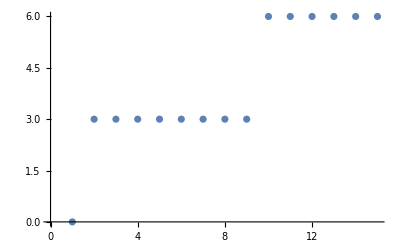

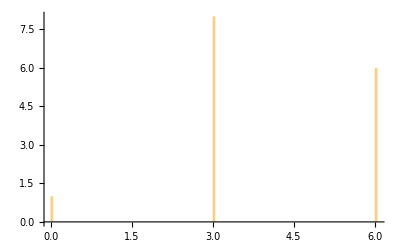

```mathematica
ListPlot[Sort[Eng]]
Histogram[Eng,100]
```

#### Some thermodynamical observables

```mathematica
Z[T_]:=Total[Exp[-1/T*Eng]];
F[T_]:=-T*Log[Z[T]];
Ene[T_]:=Total[Eng*Exp[-1/T*Eng]]/Z[T];
Ene2[T_]:=Total[Eng^2*Exp[-1/T*Eng]]/Z[T];
Cv[T_]:=-1/T^2*(Ene[T]^2-Ene2[T]);
entropy[T_]:=(Ene[T]-F[T])/T;
```

1.

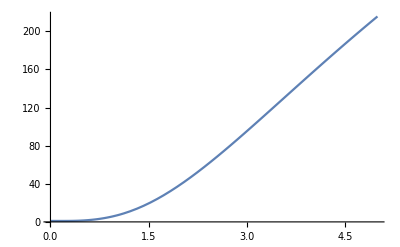

General::munfl: Exp[-14805.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13381.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13179.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

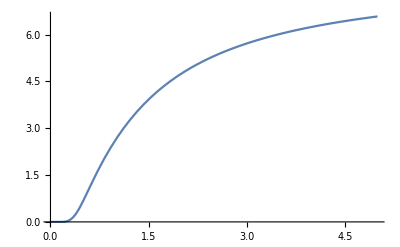

General::munfl: Exp[-14805.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13381.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13179.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

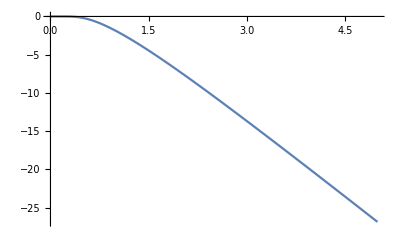

General::munfl: Exp[-14805.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13381.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13179.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

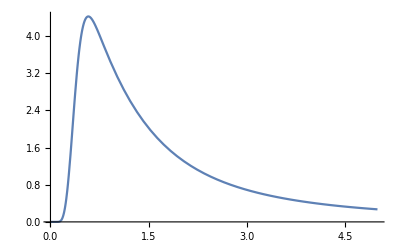

General::munfl: Exp[-14805.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13381.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13179.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

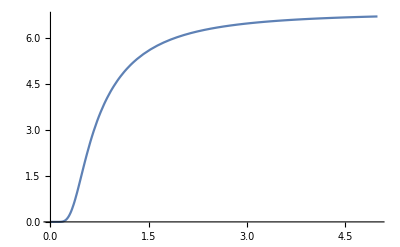

```mathematica
Z[0.00001]
Plot[Z[T],{T,0.001,5}]
Plot[Ene[T],{T,0.001,5}]
Plot[F[T],{T,0.001,5}]
Plot[Cv[T],{T,0.001,5}]
Plot[entropy[T],{T,0.001,5}]
```

```mathematica
Evec={};
For[l=1,l≤Length[sectors],l++,
	AppendTo[Evec,Eigenvectors[H[l]]]
];

Elements[O_]:=Module[{elem={}},
	For[s=1,s≤Length[sectors],s++,
		For[j=1,j≤sectors[[s]],j++,
			x=Evec[[s]][[j]];
			AppendTo[elem,x.O[s].x]
		]
	];
elem];

SzElements=Elements[SzTot];
Sz2Elements=Elements[SzTot2];
SzSz11Elements=Elements[OpSzSz11];
SzSz12Elements=Elements[OpSzSz12];
SzSz13Elements=Elements[OpSzSz13];
SzSz14Elements=Elements[OpSzSz14];
```

```mathematica
Elements[OpSzSz12]
Elements[OpSzSz13]
Elements[OpSzSz11]
```

{0.333333,0.5,0.166667,-0.222222,-0.206535,-0.460132,-0.166667,-0.0555556,-0.212211,-0.13687,-0.317585,-0.222222,0.333333,0.5,0.166667}

{0.333333,0.5,0.166667,-0.222222,-0.293465,-0.0398679,-0.333333,-0.222222,-0.0880239,-0.649509,-0.0958005,-0.0555556,0.333333,0.5,0.166667}

{0.666667,1.,0.333333,0.444444,0.5,0.5,0.5,0.277778,0.300235,0.786379,0.413386,0.277778,0.666667,1.,0.333333}

```mathematica
Hu[m_]:=N[H1[m]+u*H2[m]+Shift[m]]
```

```mathematica
Elements[H]
```

{8.,5.,5.,2.,8.,8.,8.,8.,5.,5.,5.,5.,8.,5.,5.}

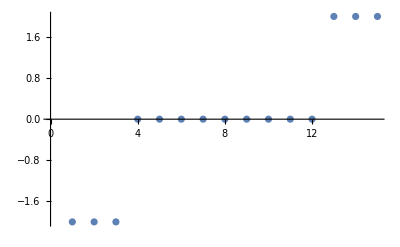

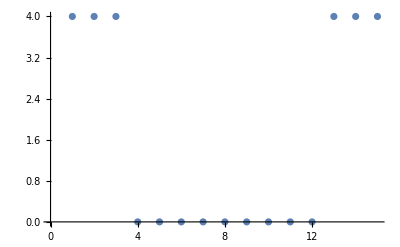

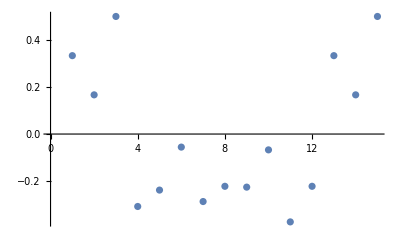

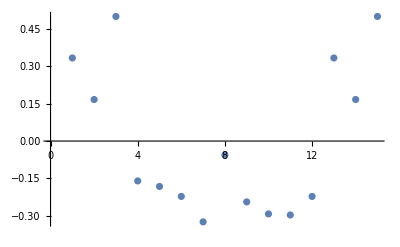

```mathematica
ListPlot[SzElements]
ListPlot[Sz2Elements]
ListPlot[SzSz12Elements]
ListPlot[SzSz13Elements]
(*ListPlot[SzSz14Elements]*)
```

```mathematica
Sz[T_]:=Total[SzElements*Exp[-1/T*Eng]]/Z[T];
Sz2[T_]:=Total[Sz2Elements*Exp[-1/T*Eng]]/Z[T];
```

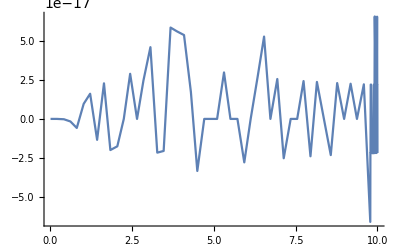

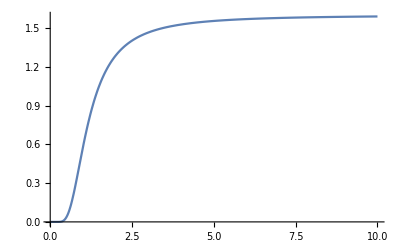

General::munfl: Exp[-19718.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

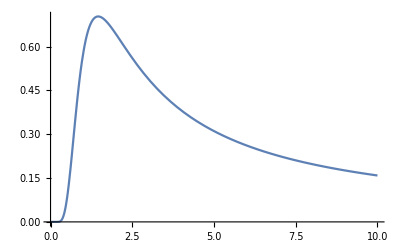

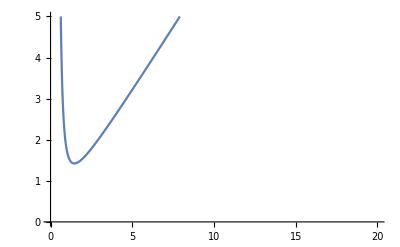

```mathematica
Plot[Sz[T],{T,0.01,10}, PlotRange->All]
Plot[Sz2[T],{T,0.01,10}, PlotRange->All]
Plot[Sz2[T]/T,{T,0.0001,10}, PlotRange->All]
Plot[T/Sz2[T],{T,0.1,20},PlotRange->{{0,20},{0,5}}]
```

#### Average double occupancy

```mathematica
SzSz11[T_]:=Total[SzSz11Elements*Exp[-1/T*Eng]]/Z[T];
SzSz12[T_]:=Total[SzSz12Elements*Exp[-1/T*Eng]]/Z[T];
SzSz13[T_]:=Total[SzSz13Elements*Exp[-1/T*Eng]]/Z[T];
SzSz14[T_]:=Total[SzSz14Elements*Exp[-1/T*Eng]]/Z[T];
```

General::munfl: Exp[-13549.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12246.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12061.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

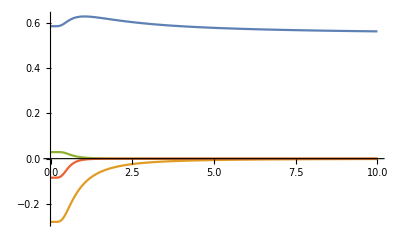

```mathematica
Plot[{SzSz11[T],SzSz12[T],SzSz13[T],SzSz14[T]},{T,0.001,10},PlotRange->Full]
```

```mathematica
Zh[T_,h_]:=Total[Exp[-1/T*(Eng-h*SzElements)]];
Szh[T_,h_]:=Total[SzElements*Exp[-1/T*(Eng-h*SzElements)]]/Zh[T,h];
```

2.44073

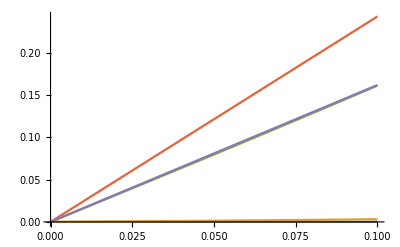

```mathematica
Szh[1,1]
Plot[{Szh[0.1,h],Szh[0.2,h],Szh[0.5,h],Szh[1,h],Szh[2,h]},{h,0,0.1}]
```

```mathematica
Manipulate[Plot[Szh[T,h],{h,0,5},PlotRange->{0,6.5}],{T,0.01,5}]
```

```mathematica
Manipulate[Plot[Szh[T,h],{h,0,0.1},PlotRange->{0,0.2}],{T,0.01,5}]
```

```mathematica
Manipulate[Plot[Szh[T,h]/h,{h,0.001,0.5},PlotRange->{0,2.5}],{T,0.01,5}]
```